# N-Channel Square Well Model

NPM

## Setup

For background, see the “CoupledSqrWellV4.nb and *V5.nb” files.  Here, I will set up a streamlined version of the code.

```mathematica
f[L_,k_,r_]=√(π/2 k r)BesselJ[L+1/2,k r];
```

```mathematica
df[L_,k_,r_]=Simplify[D[√(π/2 k r)BesselJ[L+1/2,k r],r]];
```

```mathematica
g[L_,k_,r_]=√(π/2 k r)BesselY[L+1/2,k r];
```

```mathematica
dg[L_,k_,r_]=Simplify[D[√(π/2 k r)BesselY[L+1/2,k r],r]];
```

```mathematica
gb[L_,κ_,r_]=√(π/2 κ r)BesselK[L+1/2,κ r] ⅇ^(κ Rshift)/.Rshift->0.8;
```

```mathematica
dgb[L_,κ_,r_]=Simplify[D[√(π/2 κ r)BesselK[L+1/2,κ r] ⅇ^(κ Rshift)/.Rshift->0.8,r]];
```

The setup for the two-channel case looks like

(f_o | -g_o | 0 | -ψ_11^I | -ψ_12^I
(∂f_o)/(∂r) | -(∂g_o)/(∂r) | 0 | -(∂ψ_11^I)/(∂r) | -(∂ψ_12^I)/(∂r)
0 | 0 | g_2 | -ψ_21^I | -ψ_22^I
0 | 0 | (∂g_2)/(∂r) | -(∂ψ_21^I)/(∂r) | -(∂ψ_22^I)/(∂r)
1 | 0 | 0 | 0 | 0)(c
s
a_1
b_1
b_2)=(0
0
0
0
0
1)

```mathematica
SetupPotentialW[NumChan_,v0_,ϵ1_,γ_]:=
Module[{i,j,ϵthresh},

(*ϵthresh=Table[ϵ1 (i-1),{i,1,NumChan}];*)
ϵthresh=Table[If[i==1,0,ϵ1],{i,1,NumChan}];

W=Table[If[i==j,v0,(KroneckerDelta[i,j-1]+ KroneckerDelta[i,j+1])γ],{i,1,NumChan},{j,1,NumChan}];
Avals=Simplify[Eigenvalues[W]];
AvecsNormed=Transpose[Table[FullSimplify[Normalize[Eigenvectors[W][[n]]]],{n,1,NumChan}]];
{Avals,AvecsNormed,ϵthresh,W}
]
```

```mathematica
SetupABMat[NumChan_,NumOpen_,ϵthresh_,Λ_,U_,L_,r_,ϵ_]:=
Module[{i,j,Size,ABMat,Bvec,ϕ,dϕ,ψI,dψI},
Size=2NumChan+1;
Bvec=Table[0,{i,1,Size}];
Bvec[[Size]]=1.0;
ABMat=Table[0,{i,1,Size},{j,1,Size}];


ABMat[[1,1]]=f[L,√ϵ,r];
ABMat[[1,2]]=-g[L,√ϵ,r];
ABMat[[2,1]]=df[L,√ϵ,r];
ABMat[[2,2]]=-dg[L,√ϵ,r];

Do[ABMat[[2i-1,i+1 ]]=gb[L,√(ϵthresh[[i]]-ϵ),r];
ABMat[[2i,i+1]]=dgb[L,√(ϵthresh[[i]]-ϵ),r],{i,2NumOpen,NumChan}];
ABMat[[Size,1]]=1;

ϕ=Table[f[L,√(Λ[[i]]+ϵ), r],{i,1,NumChan}];
dϕ=Table[df[L,√(Λ[[i]]+ϵ), r],{i,1,NumChan}];
ψI=Table[U[[i,j]]ϕ[[j]],{i,1,NumChan},{j,1,NumChan}];
dψI=Table[U[[i,j]]dϕ[[j]],{i,1,NumChan},{j,1,NumChan}];

Do[ABMat[[2i-1,j+(NumChan+1)]]=-ψI[[i,j]];
ABMat[[2i,j+(NumChan+1)]]=-dψI[[i,j]];,{i,1,NumChan},{j,1,NumChan}];
sols=LinearSolve[ABMat,Bvec];
sols
]
```

```mathematica
SolutionData[NumChan_,NumOpen_,ϵthresh_,sols_,L_,r_,ϵ_]:=Module[
{ascat,sigma,aclose,aLsqr,norm,δOverπ,coef,σ,i,j,δ},
ascat=-sols[[2]]/sols[[1]]/√ϵ;
norm=1/(√(sols[[1]]^2+sols[[2]]^2));
δ=ArcTan[sols[[2]]/sols[[1]]];
δOverπ=ArcTan[sols[[2]]/sols[[1]]]/π;
aclose=Table[sols[[i]],{i,NumOpen+1,NumChan+1}];
coef=Table[sols[[i]],{i,NumChan+NumOpen+1,2NumChan+1}];
σ=(4π Sin[δ]^2)/ϵ;
aLsqr=Sin[δ]^2;
{ascat,δOverπ,aLsqr,norm,aclose}]
```

```mathematica
NCHAN=5;v0=2000.0;ϵ1=1000.0;γ=200;NumOpen=1;
```

```mathematica
{Λ,U,ϵthresh,W}=SetupPotentialW[NCHAN,v0,ϵ1,γ];
```

```mathematica
MatrixForm[W];
```

```mathematica
ϵ=0.01;L=0;r=1;
```

```mathematica
sols=SetupABMat[NCHAN,NumOpen,ϵthresh,Λ,U,L,r,ϵ];
```

```mathematica
-sols[[2]]/sols[[1]]/√ϵ
```

0.983128

```mathematica
SolutionData[NCHAN,NumOpen,ϵthresh,sols,L,r,ϵ]
```

{0.983128,-0.0311937,0.00957289,0.995202,{-0.0983128,-0.319076,-0.0706234,0.785057,-0.062751}}

```mathematica
dataArray=Table[sols=SetupABMat[NCHAN,NumOpen,ϵthresh,Λ,U,L,r,ϵ];data=SolutionData[NCHAN,NumOpen,ϵthresh,sols,L,r,ϵ];Table[{ϵ,data[[n]]},{n,1,3}],{ϵ,0.0001,ϵthresh[[2]],ϵthresh[[2]]/10000.0}];
```

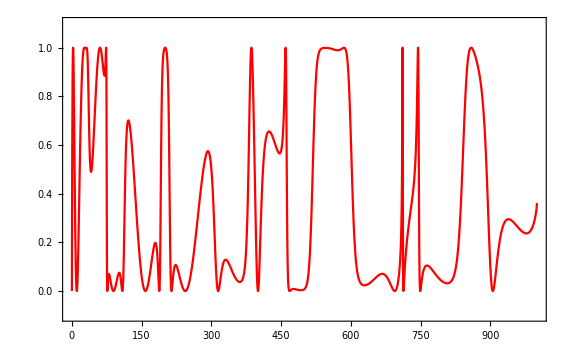

```mathematica
p1=ListPlot[Transpose[dataArray][[2]],Joined->True,PlotRange->All,PlotStyle->Black,Frame->True,LabelStyle->Large];
p2=ListPlot[Transpose[dataArray][[3]],Joined->True,PlotStyle->Red,Frame->True,LabelStyle->Large,PlotRange->{-0.1,1.1}];
Show[{p2}]
```

This next bit of code smooths out the phaseshift by adding/subtracting π at the discontinuities:

```mathematica
δdataOverπ=Transpose[dataArray][[2]];
lδ=Length[δdataOverπ];
Do[Which[
δdataOverπ[[i,2]]-δdataOverπ[[i-1,2]]>1/2, Do[δdataOverπ[[j,2]]-=1,{j,i,lδ}],
δdataOverπ[[i,2]]-δdataOverπ[[i-1,2]]<-1/2,Do[δdataOverπ[[j,2]]+=1,{j,i,lδ}]],{i,2,lδ}];
```

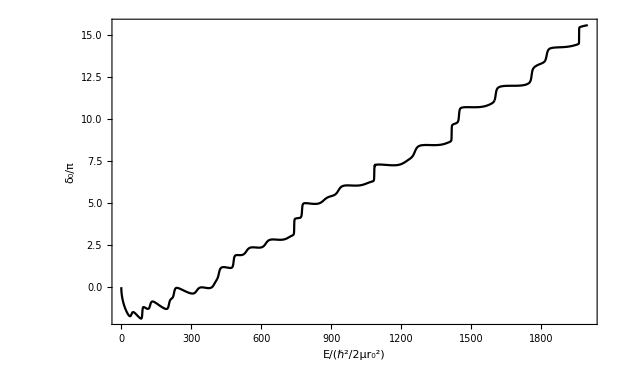

```mathematica
ListPlot[δdataOverπ,Joined->True,Frame->True,PlotStyle->Black,LabelStyle->Large,FrameLabel->{"E/(ℏ^2/2μr_0^2)","δ_0/π"}]
```

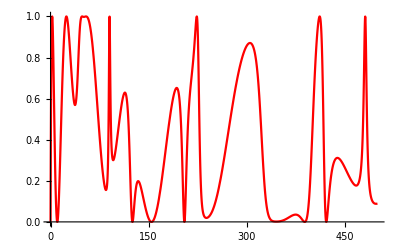

```mathematica
nσ=Plot[sols=SetupABMat[NCHAN,NumOpen,ϵthresh,Λ,U,L,r,ϵ];data=SolutionData[NCHAN,NumOpen,ϵthresh,sols,L,r,ϵ];{data[[3]]},{ϵ,0.0001,500.0},PlotStyle->{Black,Red}]
```

```mathematica
ChrisData=Import["~/Code/Nchannel/ChrisTicknor/TRINITY/result5.dat","Data"];
```

```mathematica
ChrisaL=Table[{ChrisData[[n]][[1]],ChrisData[[n]][[2]]ChrisData[[n]][[1]]/(4π)},{n,1,2002}];
```

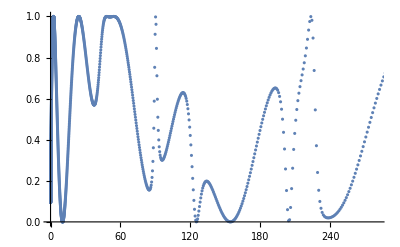

```mathematica
cσ=ListPlot[ChrisaL]
```

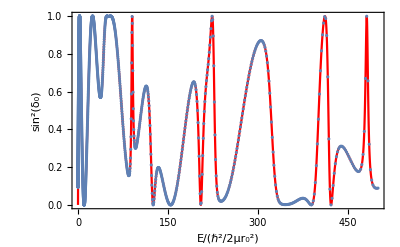

```mathematica
Show[{nσ,cσ},PlotRange->{0,1},Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","sin^2(δ_0)"},LabelStyle->Large,PlotStyle->{Red,Large}]
```

### Bound states

Let’s calculate the bound states b by diagonalizing the bound state sector only.  To do that we need to calculate the characteristic determinant for the energy eigenvalues.  We require that the wave function and derivative be continuous at the well edge.  First, define the matrix Φ with elements:

Φ_iα=U_iα f_α

This defines the interior solutions which are defined as a linear combination of these:

ψ_i^I(r)=∑_α b_α Φ_iα(r)

The exterior solutions are all decaying functions:

ψ_i^II(r)=a_i g_b(κ_i r)

Then in each channel, the log-derivative of the wave function must be continuous so we have:

[1/ψ_i^I(∂ψ_i^I)/(∂r)]_R=(1/(g_b(κ_i R))[(∂g_b)/(∂r)])_R

Define a diagonal matrix G with elements:

G_i=(1/(g_b(κ_i R))[(∂g_b)/(∂r)])_R

or...

∑_α b_α(∂Φ_iα(r))/(∂r)=G_i∑_α b_α Φ_iα(r)

and this becomes a matrix equation of the form

((∂Φ)/(∂r))_R b=G Φ b

This suggests

(((∂Φ)/(∂r))_R-G Φ)b=0

and require:

det|(((∂Φ)/(∂r))_R-G Φ)|=0

(f_o | -g_o | 0 | 0 | 0 | -ψ_11^I | -ψ_12^I | ... | -ψ_(1N)^I
(∂f_o)/(∂r) | -(∂g_o)/(∂r) | 0 | 0 | 0 | -(∂ψ_11^I)/(∂r) | -(∂ψ_12^I)/(∂r) | ... | -(∂ψ_(1N)^I)/(∂r)
0 | 0 | g_2 | 0 | 0 | -ψ_21^I | -ψ_22^I | ... | -ψ_(2N)^I
0 | 0 | (∂g_2)/(∂r) | 0 | 0 | -(∂ψ_21^I)/(∂r) | -(∂ψ_22^I)/(∂r) | ... | -(∂ψ_(2N)^I)/(∂r)
0 | 0 | 0 | ⋱ | ⋮ | ⋮ | ⋮ | ⋱ | ⋮
0 | 0 | 0 | 0 | g_N | -ψ_N1^I | -ψ_N2^I | ... | -ψ_NN^I
0 | 0 | 0 | 0 | (∂g_N)/(∂r) | -(∂ψ_N1^I)/(∂r) | -(∂ψ_N2^I)/(∂r) | ... | -(∂ψ_NN^I)/(∂r)
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)(c
s
a_2
⋮
a_N
b_1
⋮
b_N)=(0
0
0
0
0
1)

At the well edge we require

a_i g_i(R)=∑_α b_α ψ_iα(R)

a_i(∂g_i(R))/(∂r)=∑_α b_α(∂ψ_iα(R))/(∂r)

This comprises 2(N-1) unknowns (the a_is and the b_αs) and also 2(N-1) equations.  The energy eigenvalue must be determined by the normalization condition.  This may not be as simple as I had hoped...

The solution is then:

ψ_i(ϵ,r)={∑_α b_α ψ_iα(r)   if r<R
a_i g_i(r)        if r>R

Normalized in each channel according to:

```mathematica
Clear[L,k,r];
```

```mathematica
OuterNorm[L_,κ_]=FullSimplify[Integrate[gb[L,κ,r]^2,{r,1,∞}],Assumptions->κ>0]
```

1/4 π (κ BesselK[-1/2+L,κ]^2+(1+2 L) BesselK[-1/2+L,κ] BesselK[1/2+L,κ]-κ BesselK[1/2+L,κ]^2)

```mathematica
InnerNorm[L_,k_]=FullSimplify[Integrate[f[L,k,r]^2,{r,0,1}],Assumptions->L≥0]
```

1/4 k π (BesselJ[1/2+L,k]^2-BesselJ[-1/2+L,k] BesselJ[3/2+L,k])

```mathematica
TransEq[ϵ_,ϵthresh_,L_,as_,bs_]:=Module[
{i},
```

```mathematica
Clear[L];Simplify[dgb[L,κ,R]/gb[L,κ,R]]
```

-(R κ BesselK[-1/2+L,R κ]-BesselK[1/2+L,R κ]+R κ BesselK[3/2+L,R κ])/(2 R BesselK[1/2+L,R κ])

```mathematica
Needs["CUDALink`"]
```

CUDAInformation::shdw: Symbol CUDAInformation appears in multiple contexts {CUDALink`,Global`}; definitions in context CUDALink` may shadow or be shadowed by other definitions.

```mathematica
CUDAInformation[1]
```

CUDAInformation[1]

```mathematica
ℏSI=1.0545718 10^-34;hSI=ℏSI 2π;cSI=3.00 10^8;kBoltzSI=1.38064852 10^-23;amuSI=1.6605 10^-27;μSI=(m1 m2)/(m1+m2)amuSI/.{m1->23,m2->39};r0SI=4 10^-9;
```

```mathematica
ℏSI^2/(2μSI r0SI^2)/kBoltzSI
```

0.0010478

```mathematica
BNaK=0.09050 hSI cSI/kBoltzSI
```

0.00130299

```mathematica
N[3.1415926535897931-Pi]
```

0.

### Old Scratch work...

```mathematica
-sols[[2]]/sols[[1]]/√0.1
```

-0.537467

```mathematica
W=Table[If[i==j,v0-ϵ1 (i-1)/.Params,(KroneckerDelta[i,j-1]+ KroneckerDelta[i,j+1])γ/.Params],{i,1,NCHAN},{j,1,NCHAN}];
Avals=Simplify[Eigenvalues[W]];
AvecsNormed=Transpose[Table[FullSimplify[Normalize[Eigenvectors[W][[n]]]],{n,1,NCHAN}]];
```

```mathematica
ϕmat=Table[f[L,√(Avals[[i]]+ϵ), r],{i,1,NCHAN}];MatrixForm[ϕmat]
```

(√(π/2) √(r √(1.0618+ϵ)) BesselJ[1/2+L,r √(1.0618+ϵ)]
√(π/2) √(r √(0.838197+ϵ)) BesselJ[1/2+L,r √(0.838197+ϵ)])

```mathematica
dϕmat=Table[df[L,√(Avals[[i]]+ϵ), r],{i,1,NCHAN}];
```

```mathematica
ψI=Table[AvecsNormed[[i,j]]ϕmat[[j]],{i,1,NCHAN},{j,1,NCHAN} ];
dψI=D[ψI,r];
```

```mathematica
ABMAT=({{f[0,√ϵ,1], -g[0,√ϵ,1], 0, -ψI[[1,1]], -ψI[[1,2]]}, {D[f[0,√ϵ,r],r]/.r->1, -D[g[0,√ϵ,r],r]/.r->1, 0, -dψI[[1,1]], -dψI[[1,2]]}, {0, 0, gb[0,√(ϵ1-ϵ),1], -ψI[[2,1]], -ψI[[2,2]]}, {0, 0, D[gb[0,√(ϵ1-ϵ),r],r]/.r->1, -dψI[[2,1]], -dψI[[2,2]]}, {1, 0, 0, 0, 0}})/.{r->1,L->0,ϵ1->0.1}
```

```mathematica
sols=LinearSolve[ABMAT,{0,0,0,0,1}];
```

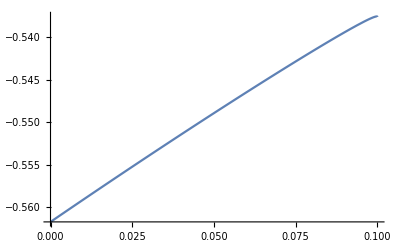

```mathematica
Plot[-sols[[2]]/sols[[1]]/√ϵ,{ϵ,0.00001,0.1}]
```